```mathematica
SetDirectory["~/MatPlay"]
IDat=Import["0531+21.csv","Table"];
```

/home/potap/MatPlay

```mathematica
IDat
```

{{0.,1724.26},{1.,1713.79},{2.,1709.61},{3.,1720.57},{4.,1722.02},{5.,1728.8},{6.,1769.84},{7.,2207.89},{8.,2943.64},{9.,3295.93},{10.,3432.54},{11.,3351.42},{12.,3264.95},{13.,3125.22},{14.,2987.11},{15.,2886.93},{16.,2801.96},{17.,2667.64},{18.,2520.39},{19.,2481.39},{20.,2397.13},{21.,2334.98},{22.,2269.58},{23.,2225.22},{24.,2200.39},{25.,2132.67},{26.,2133.89},{27.,2088.01},{28.,2039.24},{29.,2009.45},{30.,1984.97},{31.,1967.3},{32.,1932.72},{33.,1926.69},{34.,1931.23},{35.,1917.28},{36.,1902.9},{37.,1891.06},{38.,1901.78},{39.,1884.48},{40.,1900.46},{41.,1878.27},{42.,1890.81},{43.,1875.42},{44.,1869.33},{45.,1875.07},{46.,1869.14},{47.,1852.35},{48.,1857.74},{49.,1851.82},{50.,1848.3},{51.,1845.06},{52.,1832.31},{53.,1826.52},{54.,1825.42},{55.,1818.72},{56.,1810.1},{57.,1816.22},{58.,1812.71},{59.,1793.4},{60.,1801.82},{61.,1791.41},{62.,1798.16},{63.,1787.96},{64.,1781.23},{65.,1785.39},{66.,1770.35},{67.,1759.34},{68.,1777.97},{69.,1785.82},{70.,1780.14},{71.,1778.14},{72.,1755.31},{73.,1762.34},{74.,1758.35},{75.,1764.94},{76.,1750.},{77.,1761.93},{78.,1776.47},{79.,1740.29},{80.,1756.25},{81.,1760.16},{82.,1760.78},{83.,1762.23},{84.,1756.91},{85.,1748.42},{86.,1758.43},{87.,1745.53},{88.,1745.39},{89.,1749.26},{90.,1757.43},{91.,1748.26},{92.,1756.07},{93.,1756.73},{94.,1750.15},{95.,1755.48},{96.,1750.92},{97.,1738.61},{98.,1751.21},{99.,1752.42}}

```mathematica
Font1="Helvetica"
```

Helvetica

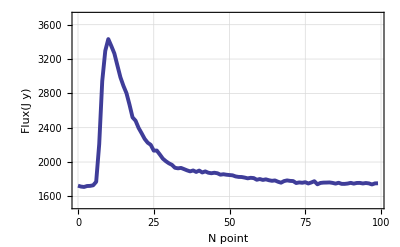

```mathematica
GP1=ListPlot[IDat,PlotRange->{All,{1500,3700}}, Axes->True,AxesOrigin->{0,1500},Frame->True,FrameLabel->{"N point","Flux(J y)"},LabelStyle->{Medium},Joined->True,PlotStyle-> Directive[Thickness[0.007]],GridLines->Automatic,GridLinesStyle->Directive[Opacity[0.5]],FrameStyle->Directive[Medium,(FontFamily->Font1)]]
```

```mathematica
Export["0531_Flux.eps",GP1,"EPS"]
```

0531_Flux.eps